# stress jump

#### Formatting the way of plotting

```mathematica
ResourceFunction["MaTeXInstall"][];
```

```mathematica
ConfigureMaTeX["Ghostscript" -> "C:\\Program Files\\gs\\gs9.54.0\\bin\\gswin64c.exe"]
```

```mathematica
(*http://szhorvat.net/pelican/latex-typesetting-in-mathematica.html*)
(*ResourceFunction["MaTeXInstall"][];*) (* <-Run  once forevere *) 
(*ConfigureMaTeX["Ghostscript" -> "C:\\Program Files\\gs\\gs9.54.0\\bin\\gswin64c.exe"]*)
Needs["MaTeX`"]
Myfontsize=22;
texStyle={FontFamily->"CMU Serif",FontSize->Myfontsize};
SetOptions[Plot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[LogLogPlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListPlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListLogPlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListLogLinearPlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListLogLogPlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListVectorPlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListLinePlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
```

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

#### Installing the post-processing module of PyFrac

```mathematica
(*PacletUninstall["PyFrac_post"]*)
mypaclet = PacletInstall["C:\\Users\\peruzzo\\Desktop\\PyFrac_Mathematica_postprocessing-main\\PyFracPost-0.0.2.paclet"]
```

PacletObject[…]

```mathematica
Needs["PostprocessPyFrac`"]
```

getFr::shdw: Symbol getFr appears in multiple contexts {getSINGLEfrac`,getDOUBLEfrac`}; definitions in context getSINGLEfrac` may shadow or be shadowed by other definitions.

Get::noopen: Cannot open DescriptionUtilities`.

Needs::nocont: Context DescriptionUtilities` was not created when Needs was evaluated.

## Importing & processing the numerical data for multiple simulations

#### Defining paths to the json files

```mathematica
commonPath ="C:\\Users\\peruzzo\\PycharmProjects\\PyFrac\\stressJump\\Data\\";
(*PathNameSimResults=StringJoin[commonPath,#]&/@{"K02_export.json","K03_export.json","K04_export.json","K05_export.json","K06_export.json","K07_export.json","K08_export.json","K09_export.json","K10_export.json","K11_export.json","K12_export.json","K14_export.json","K15_export.json","K16_export.json","K17_export.json","K18_export.json","K19_export.json","K20_export.json"};*)
PathNameSimResults=StringJoin[commonPath,#]&/@{"MK01_export.json","MK02_export.json","MK03_export.json","MK05_export.json","MK08_export.json",
"MK09_export.json","MK10_export.json","MK11_export.json","K08_export.json","MK09_export.json","MK10_export.json","MK11_export.json","MK12_export.json"};
PathNameSimResults=StringJoin[commonPath,#]&/@{"MK07_export.json"};
(*PathNameSimResults=StringJoin[commonPath,#]&/@{"K01_export.json","K02_export.json","K04_export.json","K06_export.json","K11_export.json","K14_export.json"};*)
PathNameSimResults=StringJoin[commonPath,#]&/@{"MK03_export.json","MK08_export.json","MK10_export.json","MK11_export.json","K01_export.json","K02_export.json","K04_export.json","K06_export.json","K11_export.json","K14_export.json"};
PathNameSimResults=StringJoin[commonPath,#]&/@{"MK07_export.json","MK08_export.json"};
PathNameSimResults=StringJoin[commonPath,#]&/@{"SJ_B02_export.json"};
```

#### Processing each simulation to get the results

```mathematica
SimProcessed = ParallelMap[postProcessPyfrac[#,"single_fracture"]&,PathNameSimResults];
```

```mathematica
Keys[SimProcessed[[1]]]
```

{Simpath,simulinfo,SingleFractures,times,xinj,yinj,rRightVsT,rLeftVsT,rUpVsT,rBottomVsT,LastMesh,w_A(t),pf_A(t),pf_B(t),pn_A(t),pn_B(t)}

```mathematica
Keys[SimProcessed[[1]]["simulinfo"]]
```

{Eprime,max_KIc,min_KIc,max_Sigma0,min_Sigma0,stressJump_val,viscosity,total_injection_rate,sources_coordinates_lastFR,t_max,t_min,t_touching_interface,payZoneHeight,pNetCenter_ttouch,wCenter_ttouch,dimK_ttouch,frHeight,frLength}

### Common functions

```mathematica
xandyTOxy[list1_,list2_]:=Module[{i},Table[{list1[[i]],list2[[i]]},{i,1,Length[list1]}]];

(* find Gsig *)
dSig = #["simulinfo"]["stressJump_val"]&/@SimProcessed;
Pt = #["simulinfo"]["pNetCenter_ttouch"]&/@SimProcessed;
Gsig = dSig/Pt;

GsigScaled = Gsig/Max[Gsig]
LHcolors=Blend[{Blue,Red},#]&/@GsigScaled
legendlabel=MaTeX["\\frac{\\Delta\\sigma}{P_{touch}} \\text{ [-]}",FontSize->Myfontsize];
mylegend =BarLegend[{Blend[{Blue,Red},#/Max[Gsig]]&,{0,Max[Gsig]}}, LegendLabel->legendlabel,LegendLayout->"Column"];


localQ= #["simulinfo"]["total_injection_rate"]&/@SimProcessed//N;
localEprime=#["simulinfo"]["Eprime"]&/@SimProcessed;
localKprime = #["simulinfo"]["max_KIc"]*√(32/Pi)&/@SimProcessed;
localTtouch = #["simulinfo"]["t_touching_interface"]&/@SimProcessed;
localH=#["simulinfo"]["payZoneHeight"]&/@SimProcessed;

localGsig =  dSig[[#]]*√localH[[#]]/(localKprime[[#]])&/@Range[Length[SimProcessed]];

tLst=#["times"] &/@SimProcessed;
TLst=#["simulinfo"]["t_touching_interface"] &/@SimProcessed;
tdLst=Table[tLst[[i]]/TLst[[i]](*/(134.4*(localGsig[[i]])^2+2*localGsig[[i]]+1.1)*),{i,1,Length[TLst]}];

HLst=#["simulinfo"]["payZoneHeight"] &/@SimProcessed;

tK[Kprime_,Eprime_,Q_,muprime_]:=(3.7^18 Kprime^-18 muprime^5 Q^3 Eprime^13)^(1/2);
tM[Kprime_,Eprime_,Q_,muprime_]:=(1.3^18 Kprime^-18 muprime^5 Q^3 Eprime^13)^(1/2);
Table[
Kprime=SimProcessed[[i]]["simulinfo"]["max_KIc"] √(32/Pi);
Eprime=SimProcessed[[i]]["simulinfo"]["Eprime"];
Q=SimProcessed[[i]]["simulinfo"]["total_injection_rate"];
muprime=SimProcessed[[i]]["simulinfo"]["viscosity"]12;
ttouch=SimProcessed[[i]]["simulinfo"]["t_touching_interface"];
tK[Kprime,Eprime,Q,muprime]/ttouch,{i,1,Length[SimProcessed]}]

Table[
Kprime=SimProcessed[[i]]["simulinfo"]["max_KIc"] √(32/Pi);
Eprime=SimProcessed[[i]]["simulinfo"]["Eprime"];
Q=SimProcessed[[i]]["simulinfo"]["total_injection_rate"];
muprime=SimProcessed[[i]]["simulinfo"]["viscosity"]12;
ttouch=SimProcessed[[i]]["simulinfo"]["t_touching_interface"];
tM[Kprime,Eprime,Q,muprime]/ttouch,{i,1,Length[SimProcessed]}]
```

{1.}

{RGBColor[1., 0., 0.]}

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

{52199.5}

{4.25933}

### Plotting the fracture half height

```mathematica
Kprime=SimProcessed[[1]]["simulinfo"]["max_KIc"] √(32/Pi);
Eprime=SimProcessed[[1]]["simulinfo"]["Eprime"];
Q=SimProcessed[[1]]["simulinfo"]["total_injection_rate"];
muprime=SimProcessed[[1]]["simulinfo"]["viscosity"]12;
ttouch=SimProcessed[[1]]["simulinfo"]["t_touching_interface"];

hLst=#["simulinfo"]["frHeight"] &/@SimProcessed;
hdLst=Table[hLst[[i]]/HLst[[i]],{i,1,Length[HLst]}];
hdtdplot=Table[xandyTOxy[tdLst[[i]],hdLst[[i]]],{i,1,Length[tdLst]}];
xlabel=MaTeX["\\frac{t}{t_d} \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{h}{H} \\text{ [-]}",FontSize->Myfontsize];


Show[ListLogLogPlot[hdtdplot,FrameLabel->{xlabel,ylabel},PlotStyle->LHcolors,PlotLegends->mylegend],LogLogPlot[((3Eprime Q)/(Pi Kprime √2))^(2/5)(x*ttouch)^(2/5)/HLst[[1]],{x,0.1,150},PlotStyle->{Thick,Black}],LogLogPlot[0.6976((Eprime Q^3)/muprime)^(1/9)(x*ttouch)^(4/9)/HLst[[1]],{x,0.1,150},PlotStyle->{Thick,Black}],LogLogPlot[0.6(x)^(4/9),{x,0.1,150},PlotStyle->{Thick,Black}],LogLogPlot[0.7(x)^(2/5),{x,0.1,150},PlotStyle->{Thick,Black}],PlotRange->All]
```

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

-Graphics-

### Plotting the fracture half length

```mathematica
LLst=#["simulinfo"]["frLength"] &/@SimProcessed;
LdLst=Table[LLst[[i]]/HLst[[i]],{i,1,Length[HLst]}];
Ldtdplot=Table[xandyTOxy[tdLst[[i]],LdLst[[i]]],{i,1,Length[tdLst]}];
xlabel=MaTeX["\\frac{t}{t_d} \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{L}{H} \\text{ [-]}",FontSize->Myfontsize];
Show[ListLogLogPlot[Ldtdplot,FrameLabel->{xlabel,ylabel},PlotStyle->LHcolors,PlotLegends->mylegend],LogLogPlot[((3Eprime Q)/(Pi Kprime √2))^(2/5)(x*ttouch)^(2/5)/HLst[[1]],{x,1,150},PlotStyle->{Thick,Black}],LogLogPlot[0.6976((Eprime Q^3)/muprime)^(1/9)(x*ttouch)^(4/9)/HLst[[1]],{x,1,150},PlotStyle->{Thick,Black}]]
```

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

-Graphics-

### Plotting the fracture aspect ratio

```mathematica
hLst=#["simulinfo"]["frHeight"] &/@SimProcessed;
LLst=#["simulinfo"]["frLength"] &/@SimProcessed;
arLst=Table[LLst[[i]]/hLst[[i]],{i,1,Length[HLst]}];
Ldtdplot=Table[xandyTOxy[tdLst[[i]],arLst[[i]]],{i,1,Length[tdLst]}];
xlabel=MaTeX["\\frac{t}{t_d} \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{L}{h} \\text{ [-]}",FontSize->Myfontsize];
Show[ListLogLogPlot[Ldtdplot,FrameLabel->{xlabel,ylabel},PlotStyle->LHcolors,PlotLegends->mylegend],PlotRange->{{0.1,5.5},{Automatic,Automatic}}]
```

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

The path to pdfLaTeX is not configured.

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

The path to Ghostscript is not configured.

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

-Graphics-

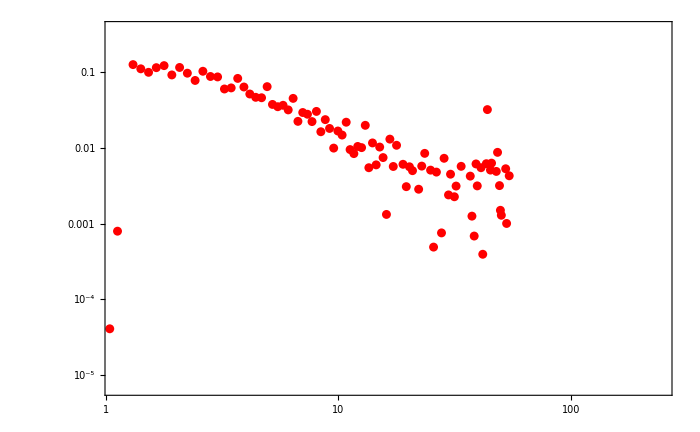

```mathematica
Plotting the rate of change of the fracture aspect ratio
GetDLdt[L_,t_]:=Module[{},Table[{(t[[i]]+t[[i-1]])/2,(L[[i]]-L[[i-1]])/(t[[i]]-t[[i-1]])},{i,2,Length[L]}]]


dLdtdplot=Table[GetDLdt[arLst[[i]],tdLst[[i]]],{i,1,Length[tdLst]}];
xlabel=MaTeX["\\frac{t}{t_d} \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{d(L/H)}{dt} \\text{ [-]}",FontSize->Myfontsize];
Show[ListLogLogPlot[dLdtdplot,FrameLabel->{xlabel,ylabel},PlotStyle->LHcolors,PlotLegends->mylegend],PlotRange->{{0.1,5.5},{-11.9,-1}}]
```

### Plotting the net pressure

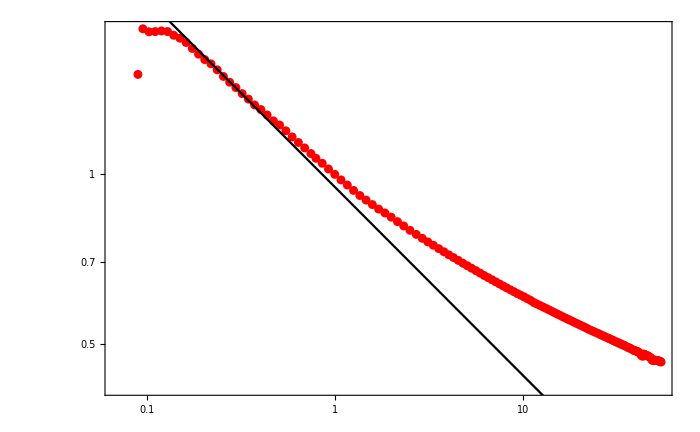

```mathematica
xlabel=MaTeX["\\frac{t}{t_d} \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{P_n}{P_{n,touch}} \\text{ [-]}",FontSize->Myfontsize];
Pdtdplot=Table[{#["pn_A(t)"][[i]][[1]]/#["simulinfo"]["t_touching_interface"],#["pn_A(t)"][[i]][[2]]/#["simulinfo"]["pNetCenter_ttouch"]},{i,1,Length[#["pn_A(t)"]]}]&/@SimProcessed;
Show[ListLogLogPlot[Pdtdplot,FrameLabel->{xlabel,ylabel},PlotStyle->LHcolors,PlotLegends->mylegend],LogLogPlot[0.95 x^(-1/3),{x,0.05,50},PlotStyle->{Thick,Black}]]
```

### Plotting the fracture width at the wellbore

{RGBColor[1., 0., 0.],RGBColor[0.3872029937377046, 0., 0.6127970062622954]}

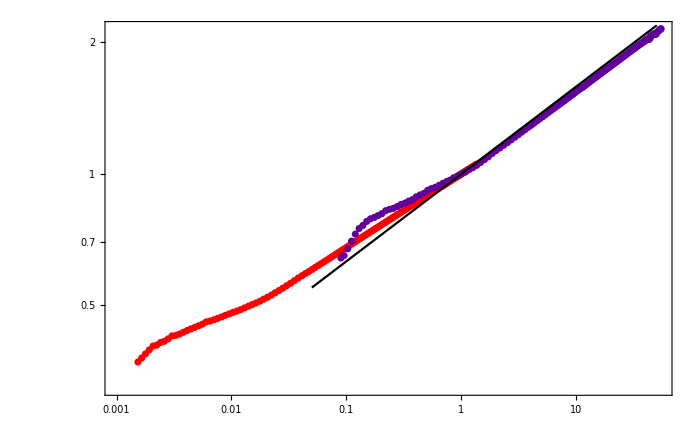

```mathematica
wdtdplot=Table[{#["w_A(t)"][[i]][[1]]/#["simulinfo"]["t_touching_interface"],#["w_A(t)"][[i]][[2]]/#["simulinfo"]["wCenter_ttouch"]},{i,1,Length[#["w_A(t)"]]}]&/@SimProcessed;
LHcolors
xlabel=MaTeX["\\frac{t}{t_d} \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{w}{w_{touch}} \\text{ [-]}",FontSize->Myfontsize];
Show[ListLogLogPlot[wdtdplot,FrameLabel->{xlabel,ylabel},PlotStyle->LHcolors,PlotLegends->mylegend],LogLogPlot[x^(1/5),{x,0.05,50},PlotStyle->{Thick,Black}]]
```

```mathematica
Plotting the rate of change of the fracture aspect ratio
```

{RGBColor[Rational[1, 3], 0, Rational[2, 3]],RGBColor[1, 0, 0]}

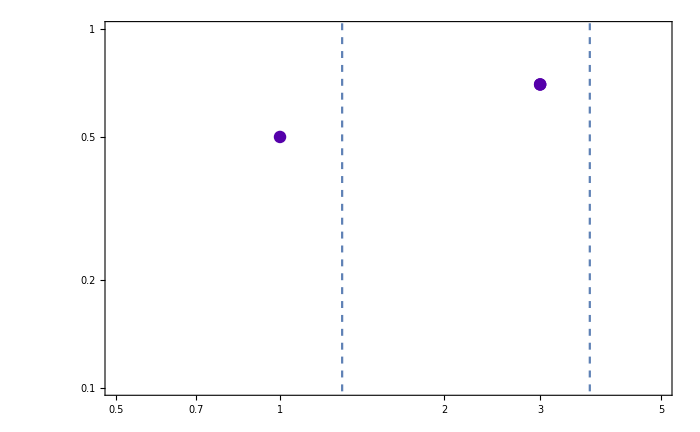

```mathematica
valueplot=Table[{{1,.5},{3,.7}},1];

timetolate ={1,3};
timetolatescaled = timetolate/Max[timetolate];
LHcolors2=Blend[{Blue,Red},#]&/@timetolatescaled
legendlabel2=MaTeX["Time to Late \\text{ [-]}",FontSize->Myfontsize];
mylegend2 =BarLegend[{Blend[{Blue,Red},#/Max[timetolate]]&,{0,Max[timetolate]}}, LegendLabel->legendlabel2,LegendLayout->"Column"];

km = 0.26236426446;(*Corresponds to K = 1.3*)
kk = 1.30833281965; (*Corresponds to K = 3.7*)
xlabel=MaTeX["\\frac{H}{L_{mk}} \\text{ [-]}",FontSize->Myfontsize];
ylabel=MaTeX["\\frac{\Delta \sigma}{P_*} \\text{ [-]}",FontSize->Myfontsize];
Show[ListLogLogPlot[valueplot,PlotRange->{{0.5,5},{.1,1}},PlotStyle->LHcolors2(*,PlotLegends->mylegend2*)],ListLinePlot[{{km,-10},{km, 3}},PlotStyle->Dashed],ListLinePlot[{{kk,-10},{kk, 3}},PlotStyle->Dashed],FrameLabel->{xlabel,ylabel}]
```